## Lesson

Compute the transpose of an array:

```mathematica
Transpose[{{1,2},{3,4}}]
```

{{1,3},{2,4}}

Create list of rules from a key and value list:

```mathematica
Thread[{1,3,5,7,9}->{2,4,6,8,10}]
```

{1→2,3→4,5→6,7→8,9→10}

Split list into sublists of given size:

```mathematica
Partition[Range[12],3]
```

{{1,2,3},{4,5,6},{7,8,9},{10,11,12}}

Flatten array:

```mathematica
Flatten[{{1,2},{3,4}}]
```

{1,2,3,4}

Create single flattened matrix from a matrix of matrices:

```mathematica
m={{1,2},{3,4}};
ArrayFlatten[{{m,m,m},{m,m,m}}]
```

{{1,2,1,2,1,2},{3,4,3,4,3,4},{1,2,1,2,1,2},{3,4,3,4,3,4}}

Split list into groups of identical elements:

```mathematica
Split[{1,1,1,2,2,1,1,3,1,1,1,2}]
```

{{1,1,1},{2,2},{1,1},{3},{1,1,1},{2}}

Gather identical elements into sublists:

```mathematica
Gather[{1,1,1,2,2,1,1,3,1,1,1,2}]
```

{{1,1,1,1,1,1,1,1},{2,2,2},{3}}

Gather by result of applying a function:

```mathematica
GatherBy[{1,1,1,2,2,1,1,3,1,1,1,2},EvenQ]
```

{{1,1,1,1,1,3,1,1,1},{2,2,2}}

Sort by result of applying a function:

```mathematica
SortBy[{1,1,1,2,2,1,1,3,1,1,1,2},EvenQ]
```

{1,1,1,1,1,1,1,1,3,2,2,2}

Introduce expression between elements of list:

```mathematica
Riffle[Range[5],x]
```

{1,x,2,x,3,x,4,x,5}

Take union of list or list of lists:

```mathematica
Union[Range[4],{1,4,6}]
```

{1,2,3,4,6}

Take intersection of list or list of lists:

```mathematica
Intersection[Range[4],{1,4,6}]
```

{1,4}

Take complement of lists:

```mathematica
Complement[Range[4],{1,4,6}]
```

{2,3}

Compute all permutations of elements of list:

```mathematica
Permutations[Range[3]]
```

{{1,2,3},{1,3,2},{2,1,3},{2,3,1},{3,1,2},{3,2,1}}

Compute all subsets of elements of list:

```mathematica
Subsets[Range[3]]
```

{{},{1},{2},{3},{1,2},{1,3},{2,3},{1,2,3}}

Compute all combinations of size n:

```mathematica
Tuples[Range[3],2]
```

{{1,1},{1,2},{1,3},{2,1},{2,2},{2,3},{3,1},{3,2},{3,3}}

Take n random choices from list:

```mathematica
RandomChoice[{2,4,6},10]
```

{6,6,4,4,4,6,2,2,4,6}

Random ordering of list:

```mathematica
RandomSample[{2,4,6}]
```

{2,4,6}

Take n non-repeating random samples:

```mathematica
RandomSample[{2,4,6},2]
```

{4,2}

## Questions

Q1. Use Thread to make a list of rules with each letter of the alphabet going to its position in the alphabet.

```mathematica
Thread[Alphabet[]->Range[26]]
```

{a→1,b→2,c→3,d→4,e→5,f→6,g→7,h→8,i→9,j→10,k→11,l→12,m→13,n→14,o→15,p→16,q→17,r→18,s→19,t→20,u→21,v→22,w→23,x→24,y→25,z→26}

Q2. Make a 4×6 grid of the first 24 letters of the alphabet.

```mathematica
Grid[Partition[Alphabet[],6]]
```

a | b | c | d | e | f
g | h | i | j | k | l
m | n | o | p | q | r
s | t | u | v | w | x

Q3. Make a grid of the digits in 2^1000, with 50 digits per row, and put frames around everything.

```mathematica
Grid[Partition[Framed/@IntegerDigits[2^1000],50]]
```

1 | 0 | 7 | 1 | 5 | 0 | 8 | 6 | 0 | 7 | 1 | 8 | 6 | 2 | 6 | 7 | 3 | 2 | 0 | 9 | 4 | 8 | 4 | 2 | 5 | 0 | 4 | 9 | 0 | 6 | 0 | 0 | 0 | 1 | 8 | 1 | 0 | 5 | 6 | 1 | 4 | 0 | 4 | 8 | 1 | 1 | 7 | 0 | 5 | 5
3 | 3 | 6 | 0 | 7 | 4 | 4 | 3 | 7 | 5 | 0 | 3 | 8 | 8 | 3 | 7 | 0 | 3 | 5 | 1 | 0 | 5 | 1 | 1 | 2 | 4 | 9 | 3 | 6 | 1 | 2 | 2 | 4 | 9 | 3 | 1 | 9 | 8 | 3 | 7 | 8 | 8 | 1 | 5 | 6 | 9 | 5 | 8 | 5 | 8
1 | 2 | 7 | 5 | 9 | 4 | 6 | 7 | 2 | 9 | 1 | 7 | 5 | 5 | 3 | 1 | 4 | 6 | 8 | 2 | 5 | 1 | 8 | 7 | 1 | 4 | 5 | 2 | 8 | 5 | 6 | 9 | 2 | 3 | 1 | 4 | 0 | 4 | 3 | 5 | 9 | 8 | 4 | 5 | 7 | 7 | 5 | 7 | 4 | 6
9 | 8 | 5 | 7 | 4 | 8 | 0 | 3 | 9 | 3 | 4 | 5 | 6 | 7 | 7 | 7 | 4 | 8 | 2 | 4 | 2 | 3 | 0 | 9 | 8 | 5 | 4 | 2 | 1 | 0 | 7 | 4 | 6 | 0 | 5 | 0 | 6 | 2 | 3 | 7 | 1 | 1 | 4 | 1 | 8 | 7 | 7 | 9 | 5 | 4
1 | 8 | 2 | 1 | 5 | 3 | 0 | 4 | 6 | 4 | 7 | 4 | 9 | 8 | 3 | 5 | 8 | 1 | 9 | 4 | 1 | 2 | 6 | 7 | 3 | 9 | 8 | 7 | 6 | 7 | 5 | 5 | 9 | 1 | 6 | 5 | 5 | 4 | 3 | 9 | 4 | 6 | 0 | 7 | 7 | 0 | 6 | 2 | 9 | 1
4 | 5 | 7 | 1 | 1 | 9 | 6 | 4 | 7 | 7 | 6 | 8 | 6 | 5 | 4 | 2 | 1 | 6 | 7 | 6 | 6 | 0 | 4 | 2 | 9 | 8 | 3 | 1 | 6 | 5 | 2 | 6 | 2 | 4 | 3 | 8 | 6 | 8 | 3 | 7 | 2 | 0 | 5 | 6 | 6 | 8 | 0 | 6 | 9 | 3

Q4. Make a grid of the first 400 characters in the Wikipedia article for “computers”, with 20 characters per row, and frames around everything.

```mathematica
Grid[Partition[Framed/@Characters[StringTake[WikipediaData["computers"],400]],20]]
```

A |   | c | o | m | p | u | t | e | r |   | i | s |   | a |   | m | a | c | h
i | n | e |   | t | h | a | t |   | c | a | n |   | b | e |   | p | r | o | g
r | a | m | m | e | d |   | t | o |   | a | u | t | o | m | a | t | i | c | a
l | l | y |   | c | a | r | r | y |   | o | u | t |   | s | e | q | u | e | n
c | e | s |   | o | f |   | a | r | i | t | h | m | e | t | i | c |   | o | r
  | l | o | g | i | c | a | l |   | o | p | e | r | a | t | i | o | n | s |  
( | c | o | m | p | u | t | a | t | i | o | n | ) | . |   | M | o | d | e | r
n |   | d | i | g | i | t | a | l |   | e | l | e | c | t | r | o | n | i | c
  | c | o | m | p | u | t | e | r | s |   | c | a | n |   | p | e | r | f | o
r | m |   | g | e | n | e | r | i | c |   | s | e | t | s |   | o | f |   | o
p | e | r | a | t | i | o | n | s |   | k | n | o | w | n |   | a | s |   | p
r | o | g | r | a | m | s | . |   | T | h | e | s | e |   | p | r | o | g | r
a | m | s |   | e | n | a | b | l | e |   | c | o | m | p | u | t | e | r | s
  | t | o |   | p | e | r | f | o | r | m |   | a |   | w | i | d | e |   | r
a | n | g | e |   | o | f |   | t | a | s | k | s | . |   | T | h | e |   | t
e | r | m |   | c | o | m | p | u | t | e | r |   | s | y | s | t | e | m |  
m | a | y |   | r | e | f | e | r |   | t | o |   | a |   | n | o | m | i | n
a | l | l | y |   | c | o | m | p | l | e | t | e |   | c | o | m | p | u | t
e | r |   | t | h | a | t |   | i | n | c | l | u | d | e | s |   | t | h | e
  | h | a | r | d | w | a | r | e | , |   | o | p | e | r | a | t | i | n | g

Q5. Make a line plot of the flattened list of the digits from the numbers from 0 to 200 (Champernowne sequence).

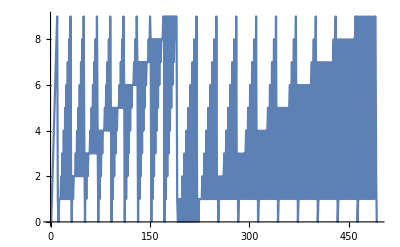

```mathematica
ListLinePlot[Flatten[IntegerDigits[Range[0,200]]]]
```

Q6. Make 4 steps in the “Menger sponge” analog of the fractal Sierpinski pattern from the text, but with a “kernel” of the form {{#, #, #}, {#, 0, #}, {#, #, #}}.

```mathematica
ArrayPlot[Nest[ArrayFlatten[{{#,#,#},{#,0,#},{#,#,#}}]&,{{1}},8]]
```

-Graphics-

Q7. Find Pythagorean triples involving only integers by selecting {x, y, Sqrt[x^2+y^2]} with x and y up to 20.

```mathematica
Flatten[Table[If[IntegerQ[√(i^2+j^2)],{i,j},Nothing],{i,20},{j,i,20}],{2}][[1]]
```

Q8. Find the lengths of the longest sequences of identical digits in 2^n for n up to 100.

```mathematica
Table[Max[Length/@Split[IntegerDigits[2^n]]],{n,100}]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,2,1,1,1,2,3,2,2,2,1,1,1,1,1,2,1,1,1,1,2,3,3,4,3,3,3,3,2,2,1,2,3,2,2,2,1,1,1,2,2,2,2,2,2,2,2,2,1,1,1,1,2,2,2,3,3,3,3,3,2,2,1,2,2,3,2,2,2,1,2,2,2,2,2,2,2,2,2,2,2,2,2}

Q9. Take the names of integers up to 100 and gather them into sublists according to their first letters.

```mathematica
GatherBy[IntegerName[Range[100]],StringTake[#,1]&]
```

{{one,one hundred},{two,three,ten,twelve,thirteen,twenty,twenty-one,twenty-two,twenty-three,twenty-four,twenty-five,twenty-six,twenty-seven,twenty-eight,twenty-nine,thirty,thirty-one,thirty-two,thirty-three,thirty-four,thirty-five,thirty-six,thirty-seven,thirty-eight,thirty-nine},{four,five,fourteen,fifteen,forty,forty-one,forty-two,forty-three,forty-four,forty-five,forty-six,forty-seven,forty-eight,forty-nine,fifty,fifty-one,fifty-two,fifty-three,fifty-four,fifty-five,fifty-six,fifty-seven,fifty-eight,fifty-nine},{six,seven,sixteen,seventeen,sixty,sixty-one,sixty-two,sixty-three,sixty-four,sixty-five,sixty-six,sixty-seven,sixty-eight,sixty-nine,seventy,seventy-one,seventy-two,seventy-three,seventy-four,seventy-five,seventy-six,seventy-seven,seventy-eight,seventy-nine},{eight,eleven,eighteen,eighty,eighty-one,eighty-two,eighty-three,eighty-four,eighty-five,eighty-six,eighty-seven,eighty-eight,eighty-nine},{nine,nineteen,ninety,ninety-one,ninety-two,ninety-three,ninety-four,ninety-five,ninety-six,ninety-seven,ninety-eight,ninety-nine}}

Q10. Sort the first 50 words in WordList[ ] by their last letters.

```mathematica
SortBy[Take[WordList[],50],StringTake[#,-1]&]
```

{a,abandoned,abashed,abbreviated,abed,abalone,abase,abate,abbe,abbreviate,abdicate,abeyance,abhorrence,abidance,abide,abducting,abiding,aah,abash,aardvark,aback,abdominal,abeam,abandon,abbreviation,abdication,abdomen,abduction,aberration,abjection,abattoir,abductor,abettor,abhor,abacus,abbess,abaft,abandonment,abasement,abashment,abatement,abbot,abduct,aberrant,abet,abhorrent,abject,abbey,ability,abjectly}

Q11. Make a list of the first 20 squares, sorted by their first digits.

```mathematica
SortBy[Range[20]^2,First[IntegerDigits[#]]&]
```

{1,16,100,121,144,169,196,25,225,256,289,36,324,361,4,49,400,64,81,9}

Q12. Sort integers up to 20 by the length of their names in English.

```mathematica
SortBy[Range[20],StringLength[IntegerName[#]]&]
```

{1,2,6,10,4,5,9,3,7,8,11,12,20,15,16,13,14,18,19,17}

Q13. Get a random sample of 20 words from WordList[ ], and gather them into sublists by length.

```mathematica
GatherBy[RandomSample[WordList[],20],StringLength]
```

{{reductionism,microbiology},{pustule,thumbed,extrude,jaybird,chicane},{rappel,snivel,ruined},{orangeade,bedspread},{sputtering,modernness,comparable,invitation},{showcase,coverall},{noncritical,bedevilment}}

Q14. Find letters that appear in Ukrainian but not Russian.

```mathematica
Complement[Alphabet["Ukrainian"],Alphabet["Russian"]]
```

{є,і,ї,ґ}

Q15. Use Intersection to find numbers that appear both among the first 100 squares and cubes.

```mathematica
Intersection[Range[100]^2,Range[100]^3]
```

{1,64,729,4096}

Q16. Find the list of countries that are in both NATO and the G8.

```mathematica
Intersection[EntityList[EntityClass["Country","NATO"]],EntityList[EntityClass["Country","GroupOf8"]]]
```

{Canada,France,Germany,Italy,United Kingdom,United States}

Q17. Make a grid in which all possible permutations of the numbers 1 through 4 appear as successive columns.

```mathematica
Grid[Transpose[Permutations[Range[4]]]]
```

1 | 1 | 1 | 1 | 1 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 4 | 4 | 4 | 4
2 | 2 | 3 | 3 | 4 | 4 | 1 | 1 | 3 | 3 | 4 | 4 | 1 | 1 | 2 | 2 | 4 | 4 | 1 | 1 | 2 | 2 | 3 | 3
3 | 4 | 2 | 4 | 2 | 3 | 3 | 4 | 1 | 4 | 1 | 3 | 2 | 4 | 1 | 4 | 1 | 2 | 2 | 3 | 1 | 3 | 1 | 2
4 | 3 | 4 | 2 | 3 | 2 | 4 | 3 | 4 | 1 | 3 | 1 | 4 | 2 | 4 | 1 | 2 | 1 | 3 | 2 | 3 | 1 | 2 | 1

Q18. Make a list of all the different strings that can be obtained by permuting the characters in “hello”.

```mathematica
StringJoin/@Permutations[Characters["hello"]]
```

{hello,helol,heoll,hlelo,hleol,hlleo,hlloe,hloel,hlole,hoell,holel,holle,ehllo,ehlol,eholl,elhlo,elhol,ellho,elloh,elohl,elolh,eohll,eolhl,eollh,lhelo,lheol,lhleo,lhloe,lhoel,lhole,lehlo,lehol,lelho,leloh,leohl,leolh,llheo,llhoe,lleho,lleoh,llohe,lloeh,lohel,lohle,loehl,loelh,lolhe,loleh,ohell,ohlel,ohlle,oehll,oelhl,oellh,olhel,olhle,olehl,olelh,ollhe,olleh}

Q19. Make an array plot of the sequence of possible 5-tuples of 0 and 1.

```mathematica
Tuples[{0,1},5]
```

{{0,0,0,0,0},{0,0,0,0,1},{0,0,0,1,0},{0,0,0,1,1},{0,0,1,0,0},{0,0,1,0,1},{0,0,1,1,0},{0,0,1,1,1},{0,1,0,0,0},{0,1,0,0,1},{0,1,0,1,0},{0,1,0,1,1},{0,1,1,0,0},{0,1,1,0,1},{0,1,1,1,0},{0,1,1,1,1},{1,0,0,0,0},{1,0,0,0,1},{1,0,0,1,0},{1,0,0,1,1},{1,0,1,0,0},{1,0,1,0,1},{1,0,1,1,0},{1,0,1,1,1},{1,1,0,0,0},{1,1,0,0,1},{1,1,0,1,0},{1,1,0,1,1},{1,1,1,0,0},{1,1,1,0,1},{1,1,1,1,0},{1,1,1,1,1}}

Q20. Generate a list of 10 random sequences of 5 letters.

```mathematica
Table[FromLetterNumber[RandomInteger[{1,26},5]],10]
```

{{o,t,u,z,o},{o,f,d,a,l},{y,k,s,a,l},{u,a,w,r,p},{q,w,l,k,z},{f,w,b,n,z},{n,y,b,o,i},{c,w,l,y,q},{m,b,m,x,l},{n,g,t,q,u}}

Q21. Find a simpler form for Flatten[Table[{i, j, k}, {i, 2}, {j, 2}, {k, 2}], 2].

```mathematica
Tuples[{1,2},3]
```

{{1,1,1},{1,1,2},{1,2,1},{1,2,2},{2,1,1},{2,1,2},{2,2,1},{2,2,2}}

## Extended Questions

+Q1. Make an array plot from the numbers of the letters in the first 1000 characters in the Wikipedia article on “computers”, with 30 letters per row.

```mathematica
ArrayPlot[Partition[LetterNumber[Characters[StringTake[WikipediaData["computers"],1000]]],30]]
```

-Graphics-

+Q2. Gather integers up to 30 into lists based on their values modulo 3.

```mathematica
GatherBy[Range[30],Mod[#,3]&]
```

{{1,4,7,10,13,16,19,22,25,28},{2,5,8,11,14,17,20,23,26,29},{3,6,9,12,15,18,21,24,27,30}}

+Q3. Gather the first 50 powers of 2 according to their last digits.

```mathematica
GatherBy[Range[50]^2,Last[IntegerDigits[#]]&]
```

{{1,81,121,361,441,841,961,1521,1681,2401},{4,64,144,324,484,784,1024,1444,1764,2304},{9,49,169,289,529,729,1089,1369,1849,2209},{16,36,196,256,576,676,1156,1296,1936,2116},{25,225,625,1225,2025},{100,400,900,1600,2500}}

+Q4. Make a line plot of the result of sorting the numbers from −10 to +10 by their absolute values.

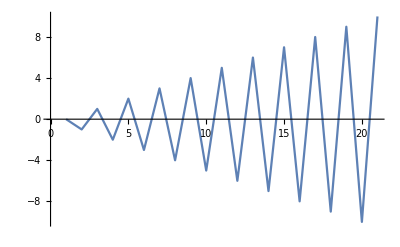

```mathematica
ListLinePlot[SortBy[Range[-10,10],Abs]]
```

+Q5. Make a line plot of the list of the first 200 squares, sorted by their first digits.

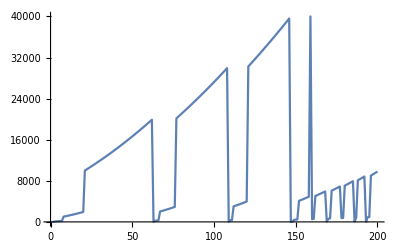

```mathematica
ListLinePlot[SortBy[Range[200]^2,First[IntegerDigits[#]]&]]
```

+Q6. Make a line plot of integers up to 200 sorted by the lengths of their names in English.

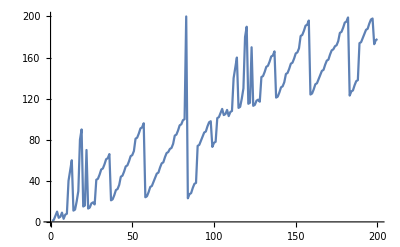

```mathematica
ListLinePlot[SortBy[Range[200],StringLength[IntegerName[#]]&]]
```

+Q7. Get a random sample of 25 words from WordList[].

```mathematica
RandomSample[WordList[],25]
```

{unanswerable,xylophone,trouper,undocumented,nettle,implode,environment,convergence,embouchure,waviness,sporting,sunstroke,blazer,ridgepole,lavaliere,actuate,softening,execution,dressy,coverage,voluminous,lynching,immature,flinch,wordplay}

+Q8. Riffle periods into the string “UNCLE” to make “U.N.C.L.E.”.

```mathematica
StringJoin[Riffle[Characters["UNCLE"],"."]]
```

U.N.C.L.E

+Q9. Find letters that appear in Swedish or Polish but not English.

```mathematica
Complement[Union[Alphabet["Swedish"],Alphabet["Polish"]],Alphabet["English"]]
```

{ą,ę,ń,ś,ź,ż,å,ä,ć,ł,ó,ö}

+Q10. Find countries that are in the World Health Organization but not the United Nations.

```mathematica
Complement[EntityList[EntityClass["Country","WorldHealthOrganization"]],EntityList[EntityClass["Country","UnitedNations"]]]
```

{Cook Islands,Niue}

+Q11. Make a list of all pair-wise blends of red, green and blue.

```mathematica
Blend/@Tuples[{Red,Green,Blue},2]
```

{RGBColor[1, 0, 0],RGBColor[Rational[1, 2], Rational[1, 2], 0],RGBColor[Rational[1, 2], 0, Rational[1, 2]],RGBColor[Rational[1, 2], Rational[1, 2], 0],RGBColor[0, 1, 0],RGBColor[0, Rational[1, 2], Rational[1, 2]],RGBColor[Rational[1, 2], 0, Rational[1, 2]],RGBColor[0, Rational[1, 2], Rational[1, 2]],RGBColor[0, 0, 1]}

```mathematica
ArrayPlot[#,ImageSize->50]&/@Partition[Tuples[{0,1},8],50]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

+Q12. Make a list of array plots, each 50 rows high and with image size 50, of successive possible 8-tuples of 0 and 1.

```mathematica
ArrayPlot[#,ImageSize->50]&/@Partition[Tuples[{0,1},8],50]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

+Q13. Generate 1000 random sequences of 4 letters, and make a list of ones that appear in WordList[ ].

```mathematica
StringJoin[Riffle[Characters["UNCLE"],"."]]
```

U.N.C.L.E

```mathematica
Table[FromLetterNumber[RandomInteger[{1,26},4]],1000]
```

{{f,v,x,f},{a,x,u,u},{y,i,n,a},{s,y,i,c},{y,q,d,r},{q,b,o,z},{t,m,u,b},{l,r,o,r},{u,i,w,p},{a,w,d,w},{j,y,t,a},{h,z,c,j},{i,y,x,b},{n,k,u,s},{p,s,e,k},{w,e,n,r},{x,h,n,p},{i,b,s,o},{a,t,t,g},{t,x,o,c},{u,g,s,r},{g,g,a,u},{j,e,x,c},{r,a,h,b},{n,d,k,u},{o,x,e,y},{u,v,m,x},{q,o,u,t},{p,a,i,q},{r,r,b,e},{l,v,w,a},{j,s,m,v},{a,a,d,b},{h,z,t,a},{s,w,y,n},{w,k,o,h},{o,y,q,t},{b,o,a,r},{p,h,g,i},{m,a,l,r},{s,e,b,l},{a,x,w,e},{w,p,o,a},{w,u,k,i},{y,j,w,l},{s,z,j,q},{w,p,v,w},{t,a,d,j},{j,l,e,b},{k,y,a,e},{y,b,t,d},{b,q,z,i},{j,j,i,c},{z,w,x,q},{g,b,x,d},{z,h,p,h},{f,x,q,k},{a,m,k,k},{f,c,v,e},{z,i,s,f},{j,q,g,u},{m,k,p,f},{d,l,t,o},{u,p,j,f},{b,a,d,n},{k,n,v,r},{v,h,v,e},{c,o,m,q},{m,w,b,p},{e,b,c,b},{r,s,v,h},{q,z,f,e},{a,e,s,s},{g,d,u,a},{f,k,g,k},{s,s,n,u},{p,z,a,l},{t,c,g,p},{a,j,t,k},{k,w,x,n},{l,e,e,a},{j,n,f,k},{a,n,f,y},{l,t,v,m},{k,d,t,i},{q,z,u,l},{r,k,b,e},{a,c,p,d},{v,j,i,x},{l,g,m,m},{c,f,q,i},{h,u,f,b},{i,j,s,m},{t,h,a,f},{j,u,n,j},{z,x,p,q},{e,n,j,f},{d,d,q,j},{e,r,b,n},{k,k,a,b},{y,a,s,g},{t,c,f,v},{g,c,r,h},{t,m,x,r},{l,l,q,i},{b,k,c,w},{p,x,v,d},{s,h,t,b},{j,l,v,b},{z,m,m,g},{x,i,p,c},{r,e,u,h},{q,m,w,d},{o,d,k,z},{h,f,s,q},{j,h,s,q},{q,m,l,b},{d,j,a,v},{c,e,i,j},{d,n,h,c},{u,t,l,j},{o,d,a,f},{v,j,v,v},{z,b,n,s},{k,o,c,g},{e,p,x,q},{m,j,b,m},{x,d,d,y},{c,m,h,p},{z,r,q,l},{g,k,o,t},{x,l,q,z},{j,m,g,x},{x,z,g,z},{f,g,j,w},{t,l,v,e},{a,g,q,y},{x,m,l,k},{f,c,r,t},{i,p,f,i},{t,l,l,p},{l,l,b,t},{h,f,n,m},{j,k,g,p},{p,o,z,p},{h,x,j,c},{v,z,e,u},{q,t,r,f},{j,s,z,r},{z,s,s,j},{f,i,a,t},{u,k,h,a},{r,o,z,p},{f,r,x,e},{l,s,x,o},{m,t,w,h},{u,w,w,a},{f,z,v,o},{t,r,r,n},{d,f,j,l},{g,u,y,v},{t,a,v,s},{d,k,i,h},{s,a,d,i},{f,k,s,y},{q,h,h,j},{x,j,x,e},{k,b,p,o},{f,d,m,n},{p,z,i,a},{l,p,w,o},{r,q,u,o},{r,p,e,g},{n,y,z,r},{g,s,z,e},{d,u,w,h},{g,c,c,j},{r,h,c,x},{p,t,p,l},{x,w,j,z},{y,e,t,p},{j,q,v,k},{k,u,b,c},{b,x,n,k},{m,x,m,v},{p,b,c,x},{o,l,j,s},{i,h,k,z},{o,b,j,k},{v,p,c,v},{d,l,g,e},{w,v,f,e},{h,w,s,i},{n,a,q,u},{y,p,d,z},{v,h,i,k},{w,n,o,r},{o,o,c,z},{d,q,p,m},{w,w,m,w},{o,f,g,u},{c,j,l,m},{u,x,u,z},{n,s,n,g},{x,u,a,p},{i,f,y,y},{c,z,t,x},{m,p,k,e},{v,y,u,b},{r,w,e,r},{v,w,z,b},{k,p,w,j},{h,t,o,z},{l,z,u,w},{s,g,o,x},{l,p,o,l},{m,o,g,l},{s,v,u,m},{o,j,e,b},{t,e,o,g},{o,y,z,x},{e,g,l,m},{k,u,e,k},{y,s,a,b},{k,l,l,i},{r,n,y,k},{o,u,v,r},{k,h,z,q},{m,b,x,e},{h,l,m,i},{j,k,s,y},{s,b,g,j},{u,d,i,k},{l,b,h,m},{w,k,a,x},{r,d,b,g},{z,f,o,z},{t,i,h,r},{a,t,c,q},{p,m,n,l},{a,j,p,n},{o,m,o,t},{v,w,a,e},{a,t,r,b},{h,w,x,i},{i,x,p,p},{s,b,e,q},{i,u,o,m},{t,u,x,j},{i,l,a,i},{b,i,b,e},{d,l,w,b},{k,h,c,z},{i,t,g,v},{j,r,u,d},{u,r,f,p},{m,r,o,p},{s,p,d,a},{h,f,n,y},{c,q,y,w},{x,f,a,l},{b,e,v,r},{z,k,z,c},{m,n,f,h},{e,n,f,i},{l,l,s,b},{t,w,w,h},{e,c,j,m},{g,b,z,q},{r,y,g,j},{z,r,r,b},{h,s,x,r},{j,m,b,b},{r,i,q,f},{i,f,c,o},{f,h,b,j},{z,g,y,h},{f,u,c,v},{n,z,h,p},{f,p,z,p},{e,b,r,o},{u,j,m,w},{f,v,v,w},{u,i,t,a},{b,n,f,n},{n,v,p,d},{a,b,v,p},{l,k,r,n},{q,o,r,c},{o,i,k,d},{w,l,n,t},{w,v,q,w},{m,o,z,n},{p,a,g,h},{z,n,c,j},{t,z,i,z},{e,a,g,l},{f,r,u,t},{t,p,c,b},{g,b,y,r},{b,i,l,w},{u,t,f,i},{v,p,c,g},{z,o,a,v},{m,q,t,p},{b,b,i,n},{x,d,b,b},{k,j,r,f},{h,q,o,l},{d,x,n,l},{k,y,y,o},{r,s,i,x},{x,p,v,q},{h,q,a,m},{v,f,q,y},{h,r,v,v},{q,e,d,o},{t,u,x,g},{z,p,s,g},{s,g,t,g},{d,v,k,k},{z,i,p,n},{e,j,z,l},{t,s,a,e},{s,b,e,k},{k,v,w,t},{y,o,b,t},{i,z,o,j},{r,f,j,o},{x,z,f,y},{z,g,o,g},{b,c,f,m},{u,r,s,z},{p,h,a,j},{f,t,z,q},{u,r,e,d},{i,r,j,d},{q,s,n,w},{y,f,d,u},{b,d,s,o},{b,b,g,c},{o,m,w,l},{m,u,j,d},{g,d,j,v},{w,q,d,t},{x,a,m,k},{u,j,k,e},{i,b,z,p},{q,e,h,g},{f,x,b,j},{x,i,f,h},{f,k,b,v},{z,g,i,s},{i,w,p,t},{e,g,u,s},{l,t,z,v},{a,o,e,c},{c,g,s,t},{x,x,g,f},{b,v,q,w},{e,e,x,g},{l,v,c,p},{b,c,z,a},{h,b,y,f},{b,c,t,h},{t,q,g,m},{b,q,v,r},{u,b,d,a},{b,j,b,x},{z,l,a,a},{t,l,h,e},{z,r,f,q},{u,l,j,y},{r,n,p,p},{g,d,g,h},{b,g,m,x},{n,o,h,t},{c,s,u,i},{m,b,r,a},{l,i,r,z},{g,x,x,f},{l,k,l,c},{m,b,p,g},{f,o,t,o},{h,b,d,k},{m,v,q,y},{m,g,v,p},{r,i,t,l},{p,m,o,c},{e,e,g,x},{z,n,r,z},{z,x,l,y},{z,z,j,z},{i,t,h,c},{p,s,w,w},{q,l,c,r},{w,x,g,h},{w,c,d,c},{j,e,h,n},{y,l,z,b},{z,c,z,e},{k,s,s,a},{m,b,o,f},{c,z,k,u},{w,p,r,g},{z,g,c,c},{g,j,a,l},{r,l,o,k},{g,k,b,l},{w,x,i,g},{u,t,i,e},{e,g,r,o},{q,b,s,a},{y,i,g,f},{x,e,q,q},{p,z,n,b},{q,z,k,t},{t,w,q,p},{q,g,c,j},{p,q,u,g},{f,v,i,z},{p,o,y,m},{k,t,n,o},{m,b,t,w},{e,c,a,i},{f,b,q,f},{z,z,s,y},{j,l,q,j},{c,j,v,q},{w,e,i,k},{l,x,d,o},{c,c,s,x},{a,m,r,q},{a,r,j,l},{z,q,n,w},{h,a,g,o},{o,y,q,n},{s,r,f,d},{h,z,r,e},{m,j,h,u},{l,w,c,m},{b,a,k,w},{o,v,y,r},{z,k,e,q},{h,m,l,g},{a,d,q,c},{r,i,y,i},{a,l,n,e},{z,g,w,n},{p,o,j,b},{k,u,e,l},{u,l,w,u},{k,p,m,v},{f,d,j,v},{o,y,b,h},{e,m,v,w},{i,h,t,q},{b,b,g,e},{v,n,p,n},{f,u,a,i},{c,s,i,o},{w,v,o,s},{u,c,l,f},{c,y,v,a},{t,y,w,y},{s,x,q,f},{v,q,v,f},{v,f,z,z},{f,l,a,f},{o,y,k,o},{t,h,v,w},{v,n,g,h},{q,o,w,n},{l,q,g,z},{a,m,g,k},{h,f,e,s},{k,d,p,z},{w,g,t,t},{e,r,a,r},{s,w,o,b},{h,r,t,m},{b,j,a,b},{t,y,r,p},{s,b,j,c},{b,z,g,m},{q,e,f,p},{a,i,x,p},{b,m,l,n},{f,r,q,t},{w,u,s,n},{b,c,r,s},{u,g,g,o},{c,b,m,c},{u,i,x,j},{v,g,t,h},{p,z,r,h},{y,e,o,l},{a,r,f,t},{g,o,l,o},{o,p,b,i},{a,h,n,e},{b,d,k,o},{i,e,z,r},{u,x,h,v},{x,x,e,d},{j,b,d,w},{e,h,x,m},{s,c,l,q},{n,e,n,e},{p,a,i,n},{h,k,h,u},{r,x,g,p},{p,r,d,s},{d,w,b,m},{h,y,x,q},{f,c,f,t},{a,a,c,k},{u,q,w,k},{c,u,b,j},{w,n,k,b},{t,l,h,z},{o,j,e,z},{y,b,f,o},{v,r,t,t},{n,j,u,e},{t,y,x,x},{q,h,b,a},{t,o,g,w},{i,l,k,k},{c,d,k,x},{h,o,l,h},{w,y,m,u},{d,y,i,h},{v,t,j,x},{p,c,l,v},{f,x,o,c},{f,p,y,r},{l,d,d,r},{e,e,v,b},{n,k,i,p},{m,z,u,b},{t,n,y,h},{g,l,z,h},{e,x,j,h},{r,g,h,f},{j,g,v,z},{u,o,w,f},{r,q,m,q},{q,t,p,d},{y,c,a,e},{s,p,f,o},{w,o,v,z},{d,o,c,x},{k,m,w,h},{r,e,l,o},{j,l,y,k},{z,i,t,n},{a,c,o,d},{b,d,s,g},{f,l,e,a},{l,m,q,p},{o,z,j,a},{w,b,q,c},{y,b,u,b},{g,r,x,j},{m,n,a,x},{v,e,g,h},{h,v,a,q},{b,x,o,g},{d,w,v,q},{g,q,d,y},{g,x,o,k},{g,w,b,x},{g,n,t,r},{a,b,a,n},{z,r,e,n},{e,q,c,s},{x,z,k,n},{q,k,w,k},{y,x,i,w},{k,k,q,c},{i,k,w,v},{j,d,h,b},{j,p,z,r},{r,y,h,i},{a,f,j,e},{x,y,e,e},{a,d,v,g},{k,c,x,j},{f,u,m,y},{c,f,l,y},{u,s,c,j},{c,d,s,h},{f,r,i,s},{e,e,n,d},{c,c,y,c},{q,l,n,i},{k,d,j,q},{k,x,m,g},{g,l,m,n},{x,v,j,e},{d,j,k,e},{f,t,z,f},{v,g,i,p},{m,e,j,s},{b,w,k,r},{c,z,f,d},{o,z,d,t},{c,v,u,i},{u,f,p,m},{w,g,g,r},{v,t,m,t},{z,b,z,l},{e,m,s,u},{n,j,i,i},{f,d,w,j},{d,n,l,w},{d,g,u,i},{k,f,w,r},{x,t,i,t},{k,l,t,x},{b,v,s,b},{k,v,w,c},{x,w,s,r},{h,x,a,w},{t,o,b,s},{t,h,n,x},{g,h,w,k},{g,z,a,n},{u,w,t,l},{h,t,p,t},{u,x,a,y},{v,h,c,u},{h,f,e,z},{d,x,w,j},{v,z,h,m},{l,p,g,q},{s,e,d,f},{l,j,x,f},{n,y,n,h},{a,w,t,x},{u,t,u,l},{i,p,d,z},{p,e,d,a},{s,t,q,v},{h,j,y,c},{r,u,e,m},{j,k,l,g},{u,q,n,m},{f,l,e,q},{a,p,g,x},{a,x,v,b},{q,e,q,s},{l,o,o,j},{g,b,s,u},{s,k,t,r},{b,e,c,z},{f,r,q,l},{o,r,a,q},{s,f,d,h},{n,z,j,y},{n,n,k,e},{e,p,f,k},{i,l,q,y},{e,g,x,c},{d,m,z,x},{i,q,u,y},{n,h,y,g},{y,q,h,a},{o,q,h,a},{t,i,i,n},{z,i,q,h},{d,b,n,b},{u,d,x,i},{v,r,e,y},{f,v,x,m},{d,f,d,c},{q,o,s,n},{n,b,c,t},{o,r,y,z},{v,z,b,o},{u,v,j,v},{y,k,a,h},{b,o,j,g},{y,w,u,i},{h,a,w,n},{m,g,n,a},{b,v,w,h},{q,p,s,h},{x,q,k,h},{v,d,z,d},{a,y,i,v},{z,w,r,x},{r,r,d,g},{e,y,f,w},{f,i,e,q},{d,v,q,c},{m,c,b,o},{g,a,m,q},{g,t,p,c},{s,t,d,l},{p,q,h,f},{i,q,m,v},{g,b,h,d},{e,s,e,y},{l,m,l,b},{y,x,r,o},{m,i,s,n},{p,r,w,m},{i,n,r,h},{x,a,o,n},{t,c,u,t},{n,l,u,i},{p,a,r,b},{f,j,o,w},{j,k,t,j},{j,f,z,c},{g,x,c,n},{u,m,a,a},{w,d,u,c},{c,s,b,e},{g,q,b,l},{n,f,r,b},{t,l,e,c},{e,y,j,l},{s,h,h,l},{z,c,c,w},{n,s,j,o},{s,p,p,e},{k,r,x,t},{a,k,s,s},{f,k,y,l},{s,a,e,n},{d,d,v,j},{m,q,t,b},{q,m,q,n},{g,k,g,z},{p,x,q,b},{w,n,r,m},{u,b,i,h},{x,a,r,d},{t,k,h,k},{v,x,f,k},{l,x,m,a},{e,o,y,a},{b,m,n,a},{o,w,y,p},{a,r,l,w},{v,a,p,y},{y,f,u,x},{e,j,f,f},{b,g,j,r},{a,q,k,r},{g,g,n,l},{n,h,x,x},{d,n,h,d},{w,d,q,i},{n,z,w,c},{j,q,v,s},{w,t,j,e},{e,v,c,f},{m,q,v,q},{d,l,t,c},{x,i,k,s},{i,i,f,t},{q,b,n,t},{a,g,y,s},{m,p,s,p},{z,w,m,v},{m,t,j,i},{l,h,v,i},{g,n,l,s},{g,x,l,z},{d,e,c,h},{g,i,k,v},{n,c,d,x},{z,x,s,k},{a,v,e,o},{t,c,q,u},{t,z,b,w},{o,v,b,f},{m,f,f,m},{u,k,d,q},{y,e,z,n},{h,f,d,g},{z,u,u,u},{m,m,l,p},{x,z,r,u},{f,e,n,m},{b,i,k,f},{g,k,x,k},{y,b,e,f},{m,p,t,h},{w,f,a,t},{e,n,n,o},{g,x,z,u},{f,h,k,o},{u,r,k,z},{t,m,y,u},{k,o,d,p},{p,j,f,f},{n,k,w,x},{c,x,r,u},{g,u,x,q},{q,s,c,f},{w,a,z,l},{l,e,q,s},{k,l,r,m},{v,o,n,p},{o,d,h,c},{l,t,w,l},{z,s,o,t},{u,s,g,w},{q,t,z,w},{t,m,n,u},{u,x,w,x},{b,b,v,m},{v,q,z,p},{b,w,h,k},{w,l,e,a},{r,b,d,r},{p,b,u,g},{v,r,e,t},{l,h,x,m},{x,s,b,n},{h,c,c,j},{q,r,a,i},{b,o,n,k},{v,r,j,y},{n,p,g,w},{p,c,z,d},{q,n,u,f},{p,x,v,y},{v,x,t,o},{b,q,y,i},{v,w,v,y},{p,o,x,y},{j,c,t,g},{l,v,s,k},{i,h,z,v},{v,a,w,h},{d,p,b,y},{i,j,o,d},{n,x,v,y},{z,c,g,i},{l,i,m,m},{h,q,e,f},{i,h,l,g},{n,f,r,e},{p,o,w,z},{n,g,o,g},{y,t,m,c},{w,n,p,z},{d,s,i,g},{c,n,l,i},{z,g,s,l},{q,a,t,f},{p,z,e,x},{c,z,a,p},{o,x,e,x},{y,t,m,e},{u,x,j,x},{h,p,f,z},{n,q,x,b},{g,a,a,k},{p,h,j,c},{x,u,w,h},{y,b,d,m},{s,n,q,n},{d,x,h,h},{o,u,f,z},{v,o,p,c},{k,n,l,g},{a,b,a,n},{i,t,n,e},{w,e,w,g},{g,f,m,v},{w,d,u,f},{o,m,q,a},{s,g,l,i},{y,e,m,g},{b,w,x,k},{q,b,y,x},{v,i,m,z},{r,h,j,c},{k,v,c,j},{w,h,j,j},{v,w,j,w},{m,q,e,j},{x,k,t,o},{p,w,l,t},{j,p,t,k},{b,q,o,z},{j,f,g,w},{j,q,t,t},{v,x,c,g},{v,c,y,j},{j,f,f,e},{h,l,a,v},{v,f,d,x},{u,d,k,u},{o,p,h,r},{t,w,f,k},{k,t,n,m},{l,p,l,d},{m,t,y,s},{b,z,k,p},{u,p,w,m},{z,m,l,q},{o,w,t,a},{m,l,l,d},{d,j,z,r},{s,z,z,o},{x,q,x,l},{m,i,c,h},{z,f,u,d},{e,b,u,w},{d,k,a,m},{s,s,s,r},{k,l,n,z},{v,y,t,i},{o,y,x,h},{p,s,p,p},{b,w,z,f},{r,s,y,n},{s,h,r,d},{q,m,l,e},{t,o,j,s},{g,f,i,b},{g,h,b,z},{u,l,b,e},{h,n,l,u},{m,s,t,y},{f,d,f,x},{y,m,v,y},{m,d,q,d},{l,e,e,n},{x,q,s,o},{c,z,i,l},{d,x,x,p},{t,u,z,y},{h,g,p,k},{z,x,n,a},{s,z,l,s},{k,g,b,u},{l,c,z,t},{z,s,z,b},{a,x,a,r},{h,x,i,v},{b,r,l,j},{n,d,a,k},{v,n,o,g},{y,a,u,k},{x,a,e,k},{i,r,a,x},{n,n,f,y},{i,z,f,j},{p,f,b,e},{b,f,x,b},{y,y,s,e},{z,c,x,l},{i,d,h,r},{w,p,z,m},{o,h,t,v},{h,p,o,o},{p,f,g,z},{d,z,l,n},{o,u,m,b},{u,s,x,s},{l,o,c,c},{i,y,m,y},{d,f,m,o},{j,k,v,k},{z,o,r,l},{e,k,n,d},{s,r,a,x},{k,u,w,t},{j,v,i,x},{l,e,x,m},{f,w,j,w},{g,m,c,q},{s,m,f,v},{q,v,q,l},{x,p,k,r},{n,d,d,a},{j,l,a,v},{t,s,e,a},{t,z,l,o},{f,i,n,d},{q,l,c,i},{x,c,q,a},{o,r,s,t},{r,s,c,i},{s,b,p,g},{g,n,a,p},{n,s,n,k},{h,f,l,t},{a,a,s,t},{m,r,n,r},{q,n,y,z}}